## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
```

```mathematica
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

```mathematica
SetDirectory[basepath<>"/output"];
```

```mathematica
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
```

```mathematica
Needs["LatticeAnalysis`"];
```

```mathematica
<<"LatticeAnalysis`"
```

```mathematica
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
lata=0.11403
```

0.11403

```mathematica
numsamples=All; (*number of samples to take for error estimates. Set to "All" if not in debug-mode!*)
```

The following line sets up blocking during the creation of Jackknife samples with block size 1.

```mathematica
MakeJacknifeSamplesB[x_]:=MakeJacknifeSamples[x,1];
```

```mathematica
thisquarkchannel="down";
```

## Constants

```mathematica
scalingNat = .1973270524; (* this is GeV*fm *)
```

```mathematica
quarkchannelshort[quarkchannel_]:=Switch[quarkchannel,"up","U","down","D","u-d","UminusD",_,Message["INVALID QUARK CHANNEL"]];
```

```mathematica
basedatapath="/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_x/"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_x/

```mathematica
exportdatapath[quarkchannel_]:=basedatapath<>quarkchannelshort[quarkchannel]<>"_";
```

```mathematica
resamplingext="_"<>"jn";
```

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
platdb1=BIDATEXReader[exportdatapath[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
```

< -MemDB- {correlatorType,gammaValue,linkPath,momTransfer,numberFilter,section,seqPropNum,sideExtent,sideLink,sideNum,sinkMom,sourceType,tSep,tSink,tSource,analysisStep,data}>

```mathematica
ensval=MemDBGet[platdb1,MemDBSelect[platdb1,{section->"ulinks",sideLink->{-2,1,3,1},sinkMom->{-1,0,0},gammaValue->8,linkPath->{1,2,1},numberFilter->Re}],data][[1]];
Print[ensval//OutputForm]
```

⟨0.6370(18)⟩_(725J)

```mathematica
AllSideLinkList = Union[MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,numberFilter->Re}],sideLink]];
vlinksidenumlist = {};
Do[
AppendTo[vlinksidenumlist,{PathToShift[AllSideLinkList[[i]],3],Length[Union[MemDBGet[platdb1,MemDBSelect[platdb1,{sideLink->AllSideLinkList[[i]]}],linkPath]]]}],{i,Length[AllSideLinkList]}];
vlinksidenumlist//MatrixForm
```

({0,0,0} | 61
{0,0,-1} | 54
{0,-1,0} | 38
{-1,0,0} | 60
{1,0,0} | 60
{0,1,0} | 38
{0,0,1} | 54
{-1,0,-1} | 54
{-1,-1,0} | 19
{1,-1,0} | 19
{-1,0,-1} | 54
{-1,-1,0} | 19
{-1,1,0} | 19
{1,-1,0} | 19
{1,1,0} | 19
{1,0,1} | 54
{-1,1,0} | 19
{1,1,0} | 19
{1,0,1} | 54
{-1,0,-2} | 6
{-1,-1,-1} | 25
{-1,1,-1} | 25
{-1,-1,-1} | 18
{-1,-2,0} | 9
{1,-2,0} | 9
{1,-1,1} | 18
{-1,-1,-1} | 14
{-2,0,-1} | 34
{-1,1,-1} | 14
{-1,-1,-1} | 14
{-2,-1,0} | 12
{-1,1,-1} | 14
{-2,1,0} | 12
{2,-1,0} | 12
{1,-1,1} | 14
{2,1,0} | 12
{1,1,1} | 14
{1,-1,1} | 14
{2,0,1} | 34
{1,1,1} | 14
{-1,1,-1} | 18
{-1,2,0} | 9
{1,2,0} | 9
{1,1,1} | 18
{1,-1,1} | 25
{1,1,1} | 25
{1,0,2} | 6
{-2,0,-2} | 6
{-1,-1,-2} | 25
{-2,-1,-1} | 25
{-1,1,-2} | 25
{-2,1,-1} | 25
{-1,-2,-1} | 18
{-2,-1,-1} | 18
{-2,-2,0} | 9
{2,-2,0} | 9
{1,-2,1} | 18
{2,-1,1} | 18
{-2,-1,-1} | 14
{-2,0,-2} | 6
{-2,-1,-1} | 15
{-2,1,-1} | 15
{-2,1,-1} | 14
{-2,-1,-1} | 14
{-2,-1,-1} | 10
{-2,-2,0} | 9
{-2,1,-1} | 14
{-2,1,-1} | 10
{-2,2,0} | 9
{2,-2,0} | 9
{2,-1,1} | 10
{2,-1,1} | 14
{2,2,0} | 9
{2,1,1} | 10
{2,1,1} | 14
{2,-1,1} | 14
{2,-1,1} | 15
{2,1,1} | 15
{2,0,2} | 6
{2,1,1} | 14
{-2,1,-1} | 18
{-1,2,-1} | 18
{-2,2,0} | 9
{2,2,0} | 9
{2,1,1} | 18
{1,2,1} | 18
{2,-1,1} | 25
{1,-1,2} | 25
{2,1,1} | 25
{1,1,2} | 25
{2,0,2} | 6
{-2,0,-3} | 6
{-2,-1,-2} | 25
{-2,-1,-2} | 25
{-2,1,-2} | 25
{-2,1,-2} | 25
{-2,-2,-1} | 18
{-2,-2,-1} | 18
{-2,-3,0} | 9
{2,-3,0} | 9
{2,-2,1} | 18
{2,-2,1} | 18
{-3,0,-2} | 6
{-3,-1,-1} | 15
{-3,1,-1} | 15
{-3,-1,-1} | 10
{-3,-2,0} | 9
{-3,1,-1} | 10
{-3,2,0} | 9
{3,-2,0} | 9
{3,-1,1} | 10
{3,2,0} | 9
{3,1,1} | 10
{3,-1,1} | 15
{3,1,1} | 15
{3,0,2} | 6
{-2,2,-1} | 18
{-2,2,-1} | 18
{-2,3,0} | 9
{2,3,0} | 9
{2,2,1} | 18
{2,2,1} | 18
{2,-1,2} | 25
{2,-1,2} | 25
{2,1,2} | 25
{2,1,2} | 25
{2,0,3} | 6
{-3,0,-3} | 6
{-2,-1,-3} | 15
{-2,-2,-2} | 14
{-2,-1,-3} | 15
{-2,-2,-2} | 14
{-3,-1,-2} | 25
{-2,1,-3} | 15
{-2,2,-2} | 14
{-2,1,-3} | 15
{-3,1,-2} | 25
{-2,2,-2} | 14
{-2,-2,-2} | 14
{-2,-3,-1} | 10
{-2,-2,-2} | 14
{-2,-3,-1} | 10
{-3,-2,-1} | 18
{-3,-3,0} | 9
{3,-3,0} | 9
{2,-3,1} | 10
{2,-2,2} | 14
{2,-3,1} | 10
{3,-2,1} | 18
{2,-2,2} | 14
{-3,0,-3} | 6
{-3,-1,-2} | 15
{-3,1,-2} | 15
{-3,-2,-1} | 10
{-3,-3,0} | 9
{-3,2,-1} | 10
{-3,3,0} | 9
{3,-3,0} | 9
{3,-2,1} | 10
{3,3,0} | 9
{3,2,1} | 10
{3,-1,2} | 15
{3,1,2} | 15
{3,0,3} | 6
{-2,2,-2} | 14
{-3,2,-1} | 18
{-2,3,-1} | 10
{-2,2,-2} | 14
{-2,3,-1} | 10
{-3,3,0} | 9
{3,3,0} | 9
{3,2,1} | 18
{2,3,1} | 10
{2,2,2} | 14
{2,3,1} | 10
{2,2,2} | 14
{2,-2,2} | 14
{3,-1,2} | 25
{2,-1,3} | 15
{2,-2,2} | 14
{2,-1,3} | 15
{3,1,2} | 25
{2,2,2} | 14
{2,1,3} | 15
{2,2,2} | 14
{2,1,3} | 15
{3,0,3} | 6
{-3,0,-4} | 6
{-3,-1,-3} | 15
{-3,-1,-3} | 15
{-3,-2,-2} | 14
{-3,-1,-3} | 15
{-3,-2,-2} | 14
{-3,1,-3} | 15
{-3,1,-3} | 15
{-3,1,-3} | 15
{-3,2,-2} | 14
{-3,2,-2} | 14
{-3,-3,-1} | 10
{-3,-2,-2} | 14
{-3,-3,-1} | 10
{-3,-2,-2} | 14
{-3,-3,-1} | 10
{-3,-4,0} | 9
{3,-4,0} | 9
{3,-3,1} | 10
{3,-3,1} | 10
{3,-3,1} | 10
{3,-2,2} | 14
{3,-2,2} | 14
{-4,0,-3} | 6
{-4,-1,-2} | 15
{-4,1,-2} | 15
{-4,-2,-1} | 10
{-4,-3,0} | 9
{-4,2,-1} | 10
{-4,3,0} | 9
{4,-3,0} | 9
{4,-2,1} | 10
{4,3,0} | 9
{4,2,1} | 10
{4,-1,2} | 15
{4,1,2} | 15
{4,0,3} | 6
{-3,2,-2} | 14
{-3,2,-2} | 14
{-3,3,-1} | 10
{-3,3,-1} | 10
{-3,3,-1} | 10
{-3,4,0} | 9
{3,4,0} | 9
{3,3,1} | 10
{3,2,2} | 14
{3,3,1} | 10
{3,2,2} | 14
{3,3,1} | 10
{3,-2,2} | 14
{3,-2,2} | 14
{3,-1,3} | 15
{3,-1,3} | 15
{3,-1,3} | 15
{3,2,2} | 14
{3,1,3} | 15
{3,2,2} | 14
{3,1,3} | 15
{3,1,3} | 15
{3,0,4} | 6
{-4,0,-4} | 6
{-3,-2,-3} | 15
{-3,-2,-3} | 15
{-3,-2,-3} | 14
{-4,-1,-3} | 15
{-3,-2,-3} | 14
{-4,-2,-2} | 14
{-3,2,-3} | 15
{-3,2,-3} | 15
{-4,1,-3} | 15
{-3,2,-3} | 14
{-4,2,-2} | 14
{-3,2,-3} | 14
{-3,-3,-2} | 10
{-3,-3,-2} | 14
{-3,-3,-2} | 10
{-3,-3,-2} | 14
{-4,-2,-2} | 14
{-4,-3,-1} | 10
{-4,-4,0} | 9
{4,-4,0} | 9
{3,-3,2} | 10
{3,-3,2} | 10
{4,-3,1} | 10
{3,-3,2} | 14
{4,-2,2} | 14
{3,-3,2} | 14
{-4,0,-4} | 6
{-4,-4,0} | 9
{-4,4,0} | 9
{4,-4,0} | 9
{4,4,0} | 9
{4,0,4} | 6
{-3,3,-2} | 14
{-4,2,-2} | 14
{-3,3,-2} | 14
{-4,3,-1} | 10
{-3,3,-2} | 10
{-3,3,-2} | 10
{-4,4,0} | 9
{4,4,0} | 9
{4,3,1} | 10
{4,2,2} | 14
{3,3,2} | 14
{3,3,2} | 10
{3,3,2} | 14
{3,3,2} | 10
{3,-2,3} | 14
{4,-2,2} | 14
{3,-2,3} | 14
{4,-1,3} | 15
{3,-2,3} | 15
{3,-2,3} | 15
{4,2,2} | 14
{3,2,3} | 14
{4,1,3} | 15
{3,2,3} | 14
{3,2,3} | 15
{3,2,3} | 15
{4,0,4} | 6
{-4,0,-5} | 6
{-4,-2,-3} | 15
{-4,-2,-3} | 15
{-3,-3,-3} | 14
{-4,-2,-3} | 14
{-4,-2,-3} | 15
{-4,-2,-3} | 14
{-4,-2,-3} | 14
{-4,2,-3} | 15
{-4,2,-3} | 15
{-4,2,-3} | 15
{-4,2,-3} | 14
{-4,2,-3} | 14
{-4,2,-3} | 14
{-3,3,-3} | 14
{-4,-3,-2} | 10
{-3,-3,-3} | 14
{-4,-3,-2} | 14
{-4,-3,-2} | 10
{-4,-3,-2} | 14
{-4,-3,-2} | 14
{-4,-3,-2} | 10
{-4,-5,0} | 9
{4,-5,0} | 9
{4,-3,2} | 10
{4,-3,2} | 10
{4,-3,2} | 10
{4,-3,2} | 14
{4,-3,2} | 14
{4,-3,2} | 14
{3,-3,3} | 14
{-5,0,-4} | 6
{-5,-4,0} | 9
{-5,4,0} | 9
{5,-4,0} | 9
{5,4,0} | 9
{5,0,4} | 6
{-3,3,-3} | 14
{-4,3,-2} | 14
{-4,3,-2} | 14
{-4,3,-2} | 14
{-4,3,-2} | 10
{-4,3,-2} | 10
{-4,3,-2} | 10
{-4,5,0} | 9
{4,5,0} | 9
{4,3,2} | 10
{4,3,2} | 14
{4,3,2} | 14
{4,3,2} | 10
{4,3,2} | 14
{3,3,3} | 14
{4,3,2} | 10
{3,-3,3} | 14
{4,-2,3} | 14
{4,-2,3} | 14
{4,-2,3} | 14
{4,-2,3} | 15
{4,-2,3} | 15
{4,-2,3} | 15
{4,2,3} | 14
{4,2,3} | 14
{4,2,3} | 15
{4,2,3} | 14
{3,3,3} | 14
{4,2,3} | 15
{4,2,3} | 15
{4,0,5} | 6
{-5,0,-5} | 6
{-4,-2,-4} | 15
{-4,-2,-4} | 15
{-4,-3,-3} | 14
{-4,-3,-3} | 14
{-5,-2,-3} | 15
{-4,-3,-3} | 14
{-4,-3,-3} | 14
{-5,-2,-3} | 14
{-4,2,-4} | 15
{-4,2,-4} | 15
{-5,2,-3} | 15
{-4,3,-3} | 14
{-5,2,-3} | 14
{-4,3,-3} | 14
{-4,3,-3} | 14
{-4,3,-3} | 14
{-4,-4,-2} | 10
{-4,-3,-3} | 14
{-4,-3,-3} | 14
{-4,-4,-2} | 10
{-4,-3,-3} | 14
{-4,-3,-3} | 14
{-5,-3,-2} | 14
{-5,-3,-2} | 10
{-5,-5,0} | 9
{5,-5,0} | 9
{4,-4,2} | 10
{4,-4,2} | 10
{5,-3,2} | 10
{4,-3,3} | 14
{5,-3,2} | 14
{4,-3,3} | 14
{4,-3,3} | 14
{4,-3,3} | 14
{-5,0,-5} | 6
{-5,-5,0} | 9
{-5,5,0} | 9
{5,-5,0} | 9
{5,5,0} | 9
{5,0,5} | 6
{-4,3,-3} | 14
{-4,3,-3} | 14
{-4,3,-3} | 14
{-5,3,-2} | 14
{-4,3,-3} | 14
{-5,3,-2} | 10
{-4,4,-2} | 10
{-4,4,-2} | 10
{-5,5,0} | 9
{5,5,0} | 9
{5,3,2} | 10
{5,3,2} | 14
{4,3,3} | 14
{4,3,3} | 14
{4,4,2} | 10
{4,3,3} | 14
{4,3,3} | 14
{4,4,2} | 10
{4,-3,3} | 14
{4,-3,3} | 14
{4,-3,3} | 14
{5,-2,3} | 14
{4,-3,3} | 14
{5,-2,3} | 15
{4,-2,4} | 15
{4,-2,4} | 15
{5,2,3} | 14
{4,3,3} | 14
{4,3,3} | 14
{5,2,3} | 15
{4,3,3} | 14
{4,3,3} | 14
{4,2,4} | 15
{4,2,4} | 15
{5,0,5} | 6
{-5,0,-6} | 6
{-5,-2,-4} | 15
{-4,-2,-5} | 15
{-5,-2,-4} | 15
{-4,-3,-4} | 14
{-4,-3,-4} | 14
{-5,-3,-3} | 14
{-5,-2,-4} | 15
{-5,-3,-3} | 14
{-5,-3,-3} | 14
{-5,-3,-3} | 14
{-5,2,-4} | 15
{-4,2,-5} | 15
{-5,2,-4} | 15
{-5,2,-4} | 15
{-5,3,-3} | 14
{-5,3,-3} | 14
{-5,3,-3} | 14
{-4,3,-4} | 14
{-5,3,-3} | 14
{-4,3,-4} | 14
{-5,-4,-2} | 10
{-4,-4,-3} | 14
{-4,-4,-3} | 14
{-5,-3,-3} | 14
{-4,-5,-2} | 10
{-5,-4,-2} | 10
{-5,-3,-3} | 14
{-5,-3,-3} | 14
{-5,-3,-3} | 14
{-5,-4,-2} | 10
{-5,-6,0} | 9
{5,-6,0} | 9
{5,-4,2} | 10
{4,-5,2} | 10
{5,-4,2} | 10
{5,-4,2} | 10
{5,-3,3} | 14
{5,-3,3} | 14
{5,-3,3} | 14
{4,-4,3} | 14
{5,-3,3} | 14
{4,-4,3} | 14
{-6,0,-5} | 6
{-6,-5,0} | 9
{-6,5,0} | 9
{6,-5,0} | 9
{6,5,0} | 9
{6,0,5} | 6
{-4,4,-3} | 14
{-5,3,-3} | 14
{-4,4,-3} | 14
{-5,3,-3} | 14
{-5,3,-3} | 14
{-5,3,-3} | 14
{-5,4,-2} | 10
{-5,4,-2} | 10
{-4,5,-2} | 10
{-5,4,-2} | 10
{-5,6,0} | 9
{5,6,0} | 9
{5,4,2} | 10
{5,3,3} | 14
{5,3,3} | 14
{5,3,3} | 14
{5,4,2} | 10
{4,5,2} | 10
{5,3,3} | 14
{4,4,3} | 14
{4,4,3} | 14
{5,4,2} | 10
{4,-3,4} | 14
{5,-3,3} | 14
{4,-3,4} | 14
{5,-3,3} | 14
{5,-3,3} | 14
{5,-3,3} | 14
{5,-2,4} | 15
{5,-2,4} | 15
{4,-2,5} | 15
{5,-2,4} | 15
{5,3,3} | 14
{5,3,3} | 14
{5,3,3} | 14
{5,2,4} | 15
{5,3,3} | 14
{4,3,4} | 14
{4,3,4} | 14
{5,2,4} | 15
{4,2,5} | 15
{5,2,4} | 15
{5,0,6} | 6
{-6,0,-6} | 6
{-5,-2,-5} | 15
{-5,-2,-5} | 15
{-5,-2,-5} | 15
{-5,-3,-4} | 14
{-5,-3,-4} | 14
{-5,-3,-4} | 14
{-6,-2,-4} | 15
{-5,-3,-4} | 14
{-5,-3,-4} | 14
{-5,2,-5} | 15
{-5,2,-5} | 15
{-5,2,-5} | 15
{-6,2,-4} | 15
{-5,3,-4} | 14
{-5,3,-4} | 14
{-5,3,-4} | 14
{-5,3,-4} | 14
{-5,3,-4} | 14
{-5,-5,-2} | 10
{-5,-4,-3} | 14
{-5,-4,-3} | 14
{-5,-4,-3} | 14
{-5,-5,-2} | 10
{-5,-5,-2} | 10
{-5,-4,-3} | 14
{-5,-4,-3} | 14
{-6,-4,-2} | 10
{-6,-6,0} | 9
{6,-6,0} | 9
{5,-5,2} | 10
{5,-5,2} | 10
{5,-5,2} | 10
{6,-4,2} | 10
{5,-4,3} | 14
{5,-4,3} | 14
{5,-4,3} | 14
{5,-4,3} | 14
{5,-4,3} | 14
{-6,0,-6} | 6
{-6,-6,0} | 9
{-6,6,0} | 9
{6,-6,0} | 9
{6,6,0} | 9
{6,0,6} | 6
{-5,4,-3} | 14
{-5,4,-3} | 14
{-5,4,-3} | 14
{-5,4,-3} | 14
{-5,4,-3} | 14
{-6,4,-2} | 10
{-5,5,-2} | 10
{-5,5,-2} | 10
{-5,5,-2} | 10
{-6,6,0} | 9
{6,6,0} | 9
{6,4,2} | 10
{5,4,3} | 14
{5,4,3} | 14
{5,5,2} | 10
{5,5,2} | 10
{5,4,3} | 14
{5,4,3} | 14
{5,4,3} | 14
{5,5,2} | 10
{5,-3,4} | 14
{5,-3,4} | 14
{5,-3,4} | 14
{5,-3,4} | 14
{5,-3,4} | 14
{6,-2,4} | 15
{5,-2,5} | 15
{5,-2,5} | 15
{5,-2,5} | 15
{5,3,4} | 14
{5,3,4} | 14
{6,2,4} | 15
{5,3,4} | 14
{5,3,4} | 14
{5,3,4} | 14
{5,2,5} | 15
{5,2,5} | 15
{5,2,5} | 15
{6,0,6} | 6
{-6,0,-7} | 4
{-5,-3,-5} | 15
{-5,-3,-5} | 15
{-6,-2,-5} | 15
{-5,-4,-4} | 14
{-5,-4,-4} | 14
{-5,-4,-4} | 14
{-6,-3,-4} | 14
{-6,-2,-5} | 15
{-6,-3,-4} | 14
{-6,-3,-4} | 14
{-5,3,-5} | 15
{-5,3,-5} | 15
{-6,2,-5} | 15
{-6,2,-5} | 15
{-6,3,-4} | 14
{-6,3,-4} | 14
{-5,4,-4} | 14
{-6,3,-4} | 14
{-5,4,-4} | 14
{-5,4,-4} | 14
{-5,-5,-3} | 10
{-5,-4,-4} | 14
{-5,-4,-4} | 14
{-5,-4,-4} | 14
{-6,-4,-3} | 14
{-5,-5,-3} | 10
{-6,-5,-2} | 10
{-6,-4,-3} | 14
{-6,-4,-3} | 14
{-6,-5,-2} | 10
{-6,-7,0} | 6
{6,-7,0} | 6
{5,-5,3} | 10
{5,-5,3} | 10
{6,-5,2} | 10
{6,-5,2} | 10
{6,-4,3} | 14
{6,-4,3} | 14
{5,-4,4} | 14
{6,-4,3} | 14
{5,-4,4} | 14
{5,-4,4} | 14
{-7,0,-6} | 4
{-7,-6,0} | 6
{-7,6,0} | 6
{7,-6,0} | 6
{7,6,0} | 6
{7,0,6} | 4
{-5,4,-4} | 14
{-5,4,-4} | 14
{-6,4,-3} | 14
{-5,4,-4} | 14
{-6,4,-3} | 14
{-6,4,-3} | 14
{-6,5,-2} | 10
{-6,5,-2} | 10
{-5,5,-3} | 10
{-5,5,-3} | 10
{-6,7,0} | 6
{6,7,0} | 6
{6,5,2} | 10
{6,4,3} | 14
{6,4,3} | 14
{6,5,2} | 10
{5,5,3} | 10
{6,4,3} | 14
{5,4,4} | 14
{5,4,4} | 14
{5,4,4} | 14
{5,5,3} | 10
{5,-4,4} | 14
{5,-4,4} | 14
{6,-3,4} | 14
{5,-4,4} | 14
{6,-3,4} | 14
{6,-3,4} | 14
{6,-2,5} | 15
{6,-2,5} | 15
{5,-3,5} | 15
{5,-3,5} | 15
{6,3,4} | 14
{6,3,4} | 14
{6,2,5} | 15
{6,3,4} | 14
{5,4,4} | 14
{5,4,4} | 14
{5,4,4} | 14
{6,2,5} | 15
{5,3,5} | 15
{5,3,5} | 15
{6,0,7} | 4
{-7,0,-7} | 4
{-6,-3,-5} | 15
{-6,-3,-5} | 15
{-6,-3,-5} | 15
{-5,-4,-5} | 14
{-6,-4,-4} | 14
{-6,-4,-4} | 14
{-6,-4,-4} | 14
{-7,-2,-5} | 15
{-6,-4,-4} | 14
{-6,-4,-4} | 14
{-6,3,-5} | 15
{-6,3,-5} | 15
{-6,3,-5} | 15
{-7,2,-5} | 15
{-6,4,-4} | 14
{-6,4,-4} | 14
{-5,4,-5} | 14
{-6,4,-4} | 14
{-6,4,-4} | 14
{-6,4,-4} | 14
{-6,-5,-3} | 10
{-5,-5,-4} | 14
{-6,-4,-4} | 14
{-6,-4,-4} | 14
{-6,-4,-4} | 14
{-6,-5,-3} | 10
{-6,-5,-3} | 10
{-6,-4,-4} | 14
{-6,-4,-4} | 14
{-7,-5,-2} | 10
{-7,-7,0} | 6
{7,-7,0} | 6
{6,-5,3} | 10
{6,-5,3} | 10
{6,-5,3} | 10
{7,-5,2} | 10
{6,-4,4} | 14
{6,-4,4} | 14
{5,-5,4} | 14
{6,-4,4} | 14
{6,-4,4} | 14
{6,-4,4} | 14
{-7,0,-7} | 4
{-7,-7,0} | 6
{-7,7,0} | 6
{7,-7,0} | 6
{7,7,0} | 6
{7,0,7} | 4
{-6,4,-4} | 14
{-6,4,-4} | 14
{-6,4,-4} | 14
{-5,5,-4} | 14
{-6,4,-4} | 14
{-6,4,-4} | 14
{-7,5,-2} | 10
{-6,5,-3} | 10
{-6,5,-3} | 10
{-6,5,-3} | 10
{-7,7,0} | 6
{7,7,0} | 6
{7,5,2} | 10
{6,4,4} | 14
{6,4,4} | 14
{6,5,3} | 10
{6,5,3} | 10
{6,4,4} | 14
{6,4,4} | 14
{6,4,4} | 14
{5,5,4} | 14
{6,5,3} | 10
{6,-4,4} | 14
{6,-4,4} | 14
{6,-4,4} | 14
{5,-4,5} | 14
{6,-4,4} | 14
{6,-4,4} | 14
{7,-2,5} | 15
{6,-3,5} | 15
{6,-3,5} | 15
{6,-3,5} | 15
{6,4,4} | 14
{6,4,4} | 14
{7,2,5} | 15
{6,4,4} | 14
{6,4,4} | 14
{6,4,4} | 14
{5,4,5} | 14
{6,3,5} | 15
{6,3,5} | 15
{6,3,5} | 15
{7,0,7} | 4
{-7,0,-8} | 2
{-6,-3,-6} | 15
{-6,-3,-6} | 15
{-7,-3,-5} | 15
{-6,-4,-5} | 14
{-6,-4,-5} | 14
{-6,-4,-5} | 14
{-7,-4,-4} | 14
{-7,-3,-5} | 15
{-7,-4,-4} | 14
{-6,3,-6} | 15
{-6,3,-6} | 15
{-7,3,-5} | 15
{-7,3,-5} | 15
{-7,4,-4} | 14
{-6,4,-5} | 14
{-6,4,-5} | 14
{-7,4,-4} | 14
{-6,4,-5} | 14
{-6,-6,-3} | 10
{-6,-5,-4} | 14
{-6,-5,-4} | 14
{-6,-5,-4} | 14
{-7,-4,-4} | 14
{-6,-6,-3} | 10
{-7,-5,-3} | 10
{-7,-4,-4} | 14
{-7,-5,-3} | 10
{-7,-8,0} | 3
{7,-8,0} | 3
{6,-6,3} | 10
{6,-6,3} | 10
{7,-5,3} | 10
{7,-5,3} | 10
{7,-4,4} | 14
{6,-5,4} | 14
{6,-5,4} | 14
{7,-4,4} | 14
{6,-5,4} | 14
{-8,0,-7} | 2
{-8,-7,0} | 3
{-8,7,0} | 3
{8,-7,0} | 3
{8,7,0} | 3
{8,0,7} | 2
{-6,5,-4} | 14
{-7,4,-4} | 14
{-6,5,-4} | 14
{-6,5,-4} | 14
{-7,4,-4} | 14
{-7,5,-3} | 10
{-7,5,-3} | 10
{-6,6,-3} | 10
{-6,6,-3} | 10
{-7,8,0} | 3
{7,8,0} | 3
{7,5,3} | 10
{7,4,4} | 14
{7,5,3} | 10
{6,6,3} | 10
{7,4,4} | 14
{6,5,4} | 14
{6,5,4} | 14
{6,5,4} | 14
{6,6,3} | 10
{6,-4,5} | 14
{7,-4,4} | 14
{6,-4,5} | 14
{6,-4,5} | 14
{7,-4,4} | 14
{7,-3,5} | 15
{7,-3,5} | 15
{6,-3,6} | 15
{6,-3,6} | 15
{7,4,4} | 14
{7,3,5} | 15
{7,4,4} | 14
{6,4,5} | 14
{6,4,5} | 14
{6,4,5} | 14
{7,3,5} | 15
{6,3,6} | 15
{6,3,6} | 15
{7,0,8} | 2
{-8,0,-8} | 2
{-6,-3,-7} | 15
{-7,-3,-6} | 15
{-6,-5,-5} | 14
{-6,-5,-5} | 14
{-7,-4,-5} | 14
{-7,-4,-5} | 14
{-8,-3,-5} | 15
{-7,-4,-5} | 14
{-6,3,-7} | 15
{-7,3,-6} | 15
{-8,3,-5} | 15
{-7,4,-5} | 14
{-6,5,-5} | 14
{-6,5,-5} | 14
{-7,4,-5} | 14
{-7,4,-5} | 14
{-6,-5,-5} | 14
{-6,-5,-5} | 14
{-7,-5,-4} | 14
{-7,-5,-4} | 14
{-6,-7,-3} | 10
{-7,-6,-3} | 10
{-7,-5,-4} | 14
{-8,-5,-3} | 10
{-8,-8,0} | 3
{8,-8,0} | 3
{6,-7,3} | 10
{7,-6,3} | 10
{8,-5,3} | 10
{7,-5,4} | 14
{6,-5,5} | 14
{6,-5,5} | 14
{7,-5,4} | 14
{7,-5,4} | 14
{-8,0,-8} | 2
{-8,-8,0} | 3
{-8,8,0} | 3
{8,-8,0} | 3
{8,8,0} | 3
{8,0,8} | 2
{-7,5,-4} | 14
{-7,5,-4} | 14
{-6,5,-5} | 14
{-6,5,-5} | 14
{-7,5,-4} | 14
{-8,5,-3} | 10
{-7,6,-3} | 10
{-6,7,-3} | 10
{-8,8,0} | 3
{8,8,0} | 3
{8,5,3} | 10
{7,5,4} | 14
{7,6,3} | 10
{6,7,3} | 10
{7,5,4} | 14
{7,5,4} | 14
{6,5,5} | 14
{6,5,5} | 14
{7,-4,5} | 14
{7,-4,5} | 14
{6,-5,5} | 14
{6,-5,5} | 14
{7,-4,5} | 14
{8,-3,5} | 15
{7,-3,6} | 15
{6,-3,7} | 15
{7,4,5} | 14
{8,3,5} | 15
{7,4,5} | 14
{7,4,5} | 14
{6,5,5} | 14
{6,5,5} | 14
{7,3,6} | 15
{6,3,7} | 15
{8,0,8} | 2
{-8,0,-9} | 1
{-7,-3,-7} | 15
{-7,-3,-7} | 15
{-7,-5,-5} | 14
{-7,-5,-5} | 14
{-7,-5,-5} | 14
{-7,-5,-5} | 14
{-8,-3,-6} | 15
{-8,-4,-5} | 14
{-7,3,-7} | 15
{-7,3,-7} | 15
{-8,3,-6} | 15
{-8,4,-5} | 14
{-7,5,-5} | 14
{-7,5,-5} | 14
{-7,5,-5} | 14
{-7,5,-5} | 14
{-7,-5,-5} | 14
{-7,-5,-5} | 14
{-7,-5,-5} | 14
{-7,-5,-5} | 14
{-7,-7,-3} | 10
{-7,-7,-3} | 10
{-8,-5,-4} | 14
{-8,-6,-3} | 10
{-8,-9,0} | 2
{8,-9,0} | 2
{7,-7,3} | 10
{7,-7,3} | 10
{8,-6,3} | 10
{8,-5,4} | 14
{7,-5,5} | 14
{7,-5,5} | 14
{7,-5,5} | 14
{7,-5,5} | 14
{-9,0,-8} | 1
{-9,-8,0} | 2
{-9,8,0} | 2
{9,-8,0} | 2
{9,8,0} | 2
{9,0,8} | 1
{-7,5,-5} | 14
{-7,5,-5} | 14
{-7,5,-5} | 14
{-7,5,-5} | 14
{-8,5,-4} | 14
{-8,6,-3} | 10
{-7,7,-3} | 10
{-7,7,-3} | 10
{-8,9,0} | 2
{8,9,0} | 2
{8,6,3} | 10
{8,5,4} | 14
{7,7,3} | 10
{7,7,3} | 10
{7,5,5} | 14
{7,5,5} | 14
{7,5,5} | 14
{7,5,5} | 14
{7,-5,5} | 14
{7,-5,5} | 14
{7,-5,5} | 14
{7,-5,5} | 14
{8,-4,5} | 14
{8,-3,6} | 15
{7,-3,7} | 15
{7,-3,7} | 15
{8,4,5} | 14
{8,3,6} | 15
{7,5,5} | 14
{7,5,5} | 14
{7,5,5} | 14
{7,5,5} | 14
{7,3,7} | 15
{7,3,7} | 15
{8,0,9} | 1
{-9,0,-9} | 1
{-7,-4,-7} | 15
{-8,-3,-7} | 15
{-7,-5,-6} | 14
{-7,-5,-6} | 14
{-8,-5,-5} | 14
{-8,-5,-5} | 14
{-8,-5,-5} | 14
{-7,4,-7} | 15
{-8,3,-7} | 15
{-8,5,-5} | 14
{-7,5,-6} | 14
{-7,5,-6} | 14
{-8,5,-5} | 14
{-8,5,-5} | 14
{-7,-6,-5} | 14
{-7,-6,-5} | 14
{-8,-5,-5} | 14
{-8,-5,-5} | 14
{-7,-7,-4} | 10
{-8,-7,-3} | 10
{-8,-5,-5} | 14
{-9,-9,0} | 2
{9,-9,0} | 2
{7,-7,4} | 10
{8,-7,3} | 10
{8,-5,5} | 14
{7,-6,5} | 14
{7,-6,5} | 14
{8,-5,5} | 14
{8,-5,5} | 14
{-9,0,-9} | 1
{-9,-9,0} | 2
{-9,9,0} | 2
{9,-9,0} | 2
{9,9,0} | 2
{9,0,9} | 1
{-8,5,-5} | 14
{-8,5,-5} | 14
{-7,6,-5} | 14
{-7,6,-5} | 14
{-8,5,-5} | 14
{-8,7,-3} | 10
{-7,7,-4} | 10
{-9,9,0} | 2
{9,9,0} | 2
{8,5,5} | 14
{8,7,3} | 10
{7,7,4} | 10
{8,5,5} | 14
{8,5,5} | 14
{7,6,5} | 14
{7,6,5} | 14
{8,-5,5} | 14
{8,-5,5} | 14
{7,-5,6} | 14
{7,-5,6} | 14
{8,-5,5} | 14
{8,-3,7} | 15
{7,-4,7} | 15
{8,5,5} | 14
{8,5,5} | 14
{8,5,5} | 14
{7,5,6} | 14
{7,5,6} | 14
{8,3,7} | 15
{7,4,7} | 15
{9,0,9} | 1
{-8,-4,-7} | 15
{-8,-4,-7} | 15
{-7,-6,-6} | 14
{-8,-5,-6} | 14
{-8,-5,-6} | 14
{-8,-5,-6} | 14
{-8,4,-7} | 15
{-8,4,-7} | 15
{-7,6,-6} | 14
{-8,5,-6} | 14
{-8,5,-6} | 14
{-8,5,-6} | 14
{-7,-6,-6} | 14
{-8,-6,-5} | 14
{-8,-6,-5} | 14
{-8,-6,-5} | 14
{-8,-7,-4} | 10
{-8,-7,-4} | 10
{8,-7,4} | 10
{8,-7,4} | 10
{7,-6,6} | 14
{8,-6,5} | 14
{8,-6,5} | 14
{8,-6,5} | 14
{-8,6,-5} | 14
{-8,6,-5} | 14
{-8,6,-5} | 14
{-7,6,-6} | 14
{-8,7,-4} | 10
{-8,7,-4} | 10
{8,7,4} | 10
{8,7,4} | 10
{8,6,5} | 14
{8,6,5} | 14
{8,6,5} | 14
{7,6,6} | 14
{8,-5,6} | 14
{8,-5,6} | 14
{8,-5,6} | 14
{7,-6,6} | 14
{8,-4,7} | 15
{8,-4,7} | 15
{8,5,6} | 14
{8,5,6} | 14
{8,5,6} | 14
{7,6,6} | 14
{8,4,7} | 15
{8,4,7} | 15
{-8,-4,-8} | 15
{-9,-4,-7} | 15
{-8,-6,-6} | 14
{-8,-6,-6} | 14
{-8,-6,-6} | 14
{-9,-5,-6} | 14
{-8,4,-8} | 15
{-9,4,-7} | 15
{-8,6,-6} | 14
{-8,6,-6} | 14
{-9,5,-6} | 14
{-8,6,-6} | 14
{-8,-6,-6} | 14
{-8,-6,-6} | 14
{-8,-6,-6} | 14
{-9,-6,-5} | 14
{-8,-8,-4} | 10
{-9,-7,-4} | 10
{8,-8,4} | 10
{9,-7,4} | 10
{8,-6,6} | 14
{8,-6,6} | 14
{9,-6,5} | 14
{8,-6,6} | 14
{-8,6,-6} | 14
{-9,6,-5} | 14
{-8,6,-6} | 14
{-8,6,-6} | 14
{-9,7,-4} | 10
{-8,8,-4} | 10
{9,7,4} | 10
{8,8,4} | 10
{9,6,5} | 14
{8,6,6} | 14
{8,6,6} | 14
{8,6,6} | 14
{8,-6,6} | 14
{9,-5,6} | 14
{8,-6,6} | 14
{8,-6,6} | 14
{9,-4,7} | 15
{8,-4,8} | 15
{9,5,6} | 14
{8,6,6} | 14
{8,6,6} | 14
{8,6,6} | 14
{9,4,7} | 15
{8,4,8} | 15
{-9,-4,-8} | 15
{-8,-6,-7} | 14
{-9,-6,-6} | 14
{-9,-6,-6} | 14
{-9,4,-8} | 15
{-8,6,-7} | 14
{-9,6,-6} | 14
{-9,6,-6} | 14
{-8,-7,-6} | 14
{-9,-6,-6} | 14
{-9,-6,-6} | 14
{-9,-8,-4} | 10
{9,-8,4} | 10
{8,-7,6} | 14
{9,-6,6} | 14
{9,-6,6} | 14
{-9,6,-6} | 14
{-9,6,-6} | 14
{-8,7,-6} | 14
{-9,8,-4} | 10
{9,8,4} | 10
{9,6,6} | 14
{9,6,6} | 14
{8,7,6} | 14
{9,-6,6} | 14
{9,-6,6} | 14
{8,-6,7} | 14
{9,-4,8} | 15
{9,6,6} | 14
{9,6,6} | 14
{8,6,7} | 14
{9,4,8} | 15
{-9,-6,-7} | 14
{-9,-6,-7} | 14
{-9,6,-7} | 14
{-9,6,-7} | 14
{-9,-7,-6} | 14
{-9,-7,-6} | 14
{9,-7,6} | 14
{9,-7,6} | 14
{-9,7,-6} | 14
{-9,7,-6} | 14
{9,7,6} | 14
{9,7,6} | 14
{9,-6,7} | 14
{9,-6,7} | 14
{9,6,7} | 14
{9,6,7} | 14
{-9,-7,-7} | 14
{-10,-6,-7} | 14
{-9,7,-7} | 14
{-10,6,-7} | 14
{-9,-7,-7} | 14
{-10,-7,-6} | 14
{9,-7,7} | 14
{10,-7,6} | 14
{-10,7,-6} | 14
{-9,7,-7} | 14
{10,7,6} | 14
{9,7,7} | 14
{10,-6,7} | 14
{9,-7,7} | 14
{10,6,7} | 14
{9,7,7} | 14
{-10,-7,-7} | 14
{-10,7,-7} | 14
{-10,-7,-7} | 14
{10,-7,7} | 14
{-10,7,-7} | 14
{10,7,7} | 14
{10,-7,7} | 14
{10,7,7} | 14)

```mathematica
AllLinkPathList = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,numberFilter->Re}],linkPath];
Print[ "Total No. linkPath = ",Length[AllLinkPathList]]
Print[ "Total No. Distinct linkPath = ",CountDistinct[AllLinkPathList]]
DistinctLinkPaths= DeleteDuplicates[AllLinkPathList];
(*Do[Print[i,") ",PathToShift[DistinctLinkPaths[[i+1]],3],"<------->",DistinctLinkPaths[[i+1]], "<------->", MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->DistinctLinkPaths[[i+1]]}],sideNum]//DeleteDuplicates],{i,CountDistinct[AllLinkPathList]-1}]*)
Print["linkPaths -> {} are skipped"];
bveclinkPathsideNumLIST={};
Do[
AppendTo[bveclinkPathsideNumLIST,{PathToShift[DistinctLinkPaths[[i+1]],3],DistinctLinkPaths[[i+1]], MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->DistinctLinkPaths[[i+1]]}],sideNum]//DeleteDuplicates}],{i,CountDistinct[AllLinkPathList]-1}]
(*bveclinkPathsideNumLIST//MatrixForm*)
bveclinkPathsideNumLISTforbL0=Select[bveclinkPathsideNumLIST,#[[1,1]]==0&];
bveclinkPathsideNumLISTforbLpositive=Select[bveclinkPathsideNumLIST,#[[1,1]]>0&& #[[2]]!={1,2,1,1,2,1,2,1,1,2}&];
Print["linkPath -> {1,2,1,1,2,1,2,1,1,2} is skipped"];
bveclinkPathsideNumLISTforbLnegative=Select[bveclinkPathsideNumLIST,#[[1,1]]<0&& #[[1,1]]!=-7 &];
Print["linkPath corresponding to b1 = -7 is skipped"];
b2list= Union[bveclinkPathsideNumLIST[[All,1]][[All,2]]];
b1listall= Union[bveclinkPathsideNumLIST[[All,1]][[All,1]]];
b1list = Select[b1listall,#!=-7&];
Print["b2 = ",b2list]
Print["b1 = ",b1list]
bveclinkPathsideNumLISTforbL0//MatrixForm
bveclinkPathsideNumLISTforbLpositive//MatrixForm
bveclinkPathsideNumLISTforbLnegative//MatrixForm
bveclinkPathsideNumLISTforbL0//Length
bveclinkPathsideNumLISTforbLpositive//Length
bveclinkPathsideNumLISTforbLnegative//Length
noError=True;
Do[If[(bveclinkPathsideNumLISTforbLpositive[[i,1]][[1]]+bveclinkPathsideNumLISTforbLnegative[[i,1]][[1]])=!=0,Print["Mismatch in finding   at bveclinkPathsideNumLISTforbLpositive[",i, "]"];noError=False;],{i,Length[bveclinkPathsideNumLISTforbLpositive]}];
If[noError,Print["✓ Checked: linkPaths corresponding to   are found "]];
```

Total No. linkPath = 27545

Total No. Distinct linkPath = 61

linkPaths -> {} are skipped

linkPath -> {1,2,1,1,2,1,2,1,1,2} is skipped

linkPath corresponding to b1 = -7 is skipped

b2 = {1,2,3,4,5,6}

b1 = {-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6}

({0,1,0} | {2} | {0,1,16,17,18,19,20,21,22,23,24,25}
{0,2,0} | {2,2} | {0,1}
{0,3,0} | {2,2,2} | {0,1}
{0,4,0} | {2,2,2,2} | {0,1}
{0,5,0} | {2,2,2,2,2} | {0,1}
{0,6,0} | {2,2,2,2,2,2} | {0,1})

({1,1,0} | {2,1} | {0,21,22,23,24,25,4,5,11,12,13,14,15,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{1,1,0} | {1,2} | {0,21,22,23,24,25,4,5,11,12,13,14,15,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{2,1,0} | {1,2,1} | {0,4,5,11,12,13,14,15,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{3,2,0} | {1,2,1,2,1} | {0,4,5,11,12,13,14,15,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{4,2,0} | {1,2,1,1,2,1} | {0,4,5,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{4,3,0} | {1,2,1,2,1,2,1} | {0,4,5,11,12,13,14,15,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{6,3,0} | {1,2,1,1,2,1,1,2,1} | {0,4,5,11,12,13,14,15}
{6,4,0} | {1,2,1,2,1,1,2,1,2,1} | {0,4,5,11,12,13,14,15}
{2,2,0} | {1,2,1,2} | {0,21,22,23,24,25,11,12,13,14,15}
{2,2,0} | {2,1,2,1} | {0,21,22,23,24,25,11,12,13,14,15}
{5,4,0} | {1,2,1,2,1,2,1,2,1} | {0,11,12,13,14,15,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{1,2,0} | {2,1,2} | {0,21,22,23,24,25}
{2,3,0} | {2,1,2,1,2} | {0,21,22,23,24,25}
{3,3,0} | {1,2,1,2,1,2} | {0,21,22,23,24,25,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{3,3,0} | {2,1,2,1,2,1} | {0,21,22,23,24,25,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{2,4,0} | {2,1,2,2,1,2} | {0,21,22,23,24,25}
{3,4,0} | {2,1,2,1,2,1,2} | {0,21,22,23,24,25}
{2,5,0} | {2,1,2,2,2,1,2} | {0,21,22,23,24,25}
{4,5,0} | {2,1,2,1,2,1,2,1,2} | {0,21,22,23,24,25}
{4,6,0} | {2,1,2,1,2,2,1,2,1,2} | {0,21,22,23,24,25}
{5,6,0} | {2,1,2,1,2,1,2,1,2,1,2} | {0,21,22,23,24,25}
{4,4,0} | {1,2,1,2,1,2,1,2} | {0,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{4,4,0} | {2,1,2,1,2,1,2,1} | {0,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{5,5,0} | {1,2,1,2,1,2,1,2,1,2} | {0,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{5,5,0} | {2,1,2,1,2,1,2,1,2,1} | {0,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65}
{6,5,0} | {1,2,1,2,1,2,1,2,1,2,1} | {0,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65})

({-1,1,0} | {2,-1} | {0,16,17,18,19,20,2,3,6,7,8,9,10,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-1,1,0} | {-1,2} | {0,16,17,18,19,20,2,3,6,7,8,9,10,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-2,1,0} | {-1,2,-1} | {0,2,3,6,7,8,9,10,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-3,2,0} | {-1,2,-1,2,-1} | {0,2,3,6,7,8,9,10,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-4,2,0} | {-1,2,-1,-1,2,-1} | {0,2,3,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-4,3,0} | {-1,2,-1,2,-1,2,-1} | {0,2,3,6,7,8,9,10,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-6,3,0} | {-1,2,-1,-1,2,-1,-1,2,-1} | {0,2,3,6,7,8,9,10}
{-6,4,0} | {-1,2,-1,2,-1,-1,2,-1,2,-1} | {0,2,3,6,7,8,9,10}
{-2,2,0} | {-1,2,-1,2} | {0,16,17,18,19,20,6,7,8,9,10}
{-2,2,0} | {2,-1,2,-1} | {0,16,17,18,19,20,6,7,8,9,10}
{-5,4,0} | {-1,2,-1,2,-1,2,-1,2,-1} | {0,6,7,8,9,10,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-1,2,0} | {2,-1,2} | {0,16,17,18,19,20}
{-2,3,0} | {2,-1,2,-1,2} | {0,16,17,18,19,20}
{-3,3,0} | {-1,2,-1,2,-1,2} | {0,16,17,18,19,20,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-3,3,0} | {2,-1,2,-1,2,-1} | {0,16,17,18,19,20,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-2,4,0} | {2,-1,2,2,-1,2} | {0,16,17,18,19,20}
{-3,4,0} | {2,-1,2,-1,2,-1,2} | {0,16,17,18,19,20}
{-2,5,0} | {2,-1,2,2,2,-1,2} | {0,16,17,18,19,20}
{-4,5,0} | {2,-1,2,-1,2,-1,2,-1,2} | {0,16,17,18,19,20}
{-4,6,0} | {2,-1,2,-1,2,2,-1,2,-1,2} | {0,16,17,18,19,20}
{-5,6,0} | {2,-1,2,-1,2,-1,2,-1,2,-1,2} | {0,16,17,18,19,20}
{-4,4,0} | {-1,2,-1,2,-1,2,-1,2} | {0,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-4,4,0} | {2,-1,2,-1,2,-1,2,-1} | {0,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-5,5,0} | {-1,2,-1,2,-1,2,-1,2,-1,2} | {0,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-5,5,0} | {2,-1,2,-1,2,-1,2,-1,2,-1} | {0,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}
{-6,5,0} | {-1,2,-1,2,-1,2,-1,2,-1,2,-1} | {0,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45})

6

26

26

✓ Checked: linkPaths corresponding to   are found

```mathematica
Print["PlateauRange = {9,10,11,12}"];
PlateauRange={9,10,11,12};
TablePlateauEvengPlusImForb = {};
Do[
PlateauEvengPlusIm=0;
count=0;
Do[
(*If[ bveclinkPathsideNumLISTforbL0[[i,3]][[sideNumj]]== 0,Continue[]];*)
bl0g8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bveclinkPathsideNumLISTforbL0[[i,2]],sideNum-> bveclinkPathsideNumLISTforbL0[[i,3]][[sideNumj]],numberFilter->Im}],{sideExtent,data}];
bl0g1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->bveclinkPathsideNumLISTforbL0[[i,2]],sideNum-> bveclinkPathsideNumLISTforbL0[[i,3]][[sideNumj]],numberFilter->Re}],{sideExtent,data}];
etaList = bl0g8Im[[All,1]];
If[ Round[((Length[etaList]-1)/2)]< Max[PlateauRange],Continue[]];
bl0gPlusIm = (bl0g1Re[[All, 2]]+bl0g8Im[[All, 2]])/Sqrt[2];
PlotblEvengPlusIm=Transpose[{etaList,bl0gPlusIm}];
(*PlateauRange=Table[(Round[((Length[etaList]-1)/2)]-4+n),{n,0,4}];
Print["Averaging  values: ",PlateauRange];*)
     PlateauPluseta = 0;
PlateauMinuseta = 0;
Do[
blEvengPlusImEta=Select[PlotblEvengPlusIm,#[[1]]==PlateauEta&][[All,2]];
blEvengMinusImEta=Select[PlotblEvengPlusIm,#[[1]]==-PlateauEta&][[All,2]];

PlateauPluseta+=blEvengPlusImEta/Length[PlateauRange];
PlateauMinuseta+=blEvengMinusImEta/Length[PlateauRange];

,{PlateauEta, PlateauRange}];
PlateauEvengPlusImsideNumj = (-PlateauMinuseta+PlateauPluseta)/2;
(*Print[bveclinkPathsideNumLISTforbL0[[i,1]]," ",bveclinkPathsideNumLISTforbL0[[i,3]][[sideNumj]]," ",PlateauEvengPlusImsideNumj//OutputForm];*)
(*PlateauEvengPlusIm += PlateauEvengPlusImsideNumj/(Length[bveclinkPathsideNumLISTforbL0[[i,3]]]); (*-1 because we are skipping sideNum 0*)*)
PlateauEvengPlusIm += PlateauEvengPlusImsideNumj;
count += 1;
,{sideNumj, Length[bveclinkPathsideNumLISTforbL0[[i,3]]]}];
If[ count==0,Continue[]];
AppendTo[TablePlateauEvengPlusImForb,{bveclinkPathsideNumLISTforbL0[[i,1]],PlateauEvengPlusIm[[1]]/count}];
  ,{i,Length[bveclinkPathsideNumLISTforbL0]}];

Do[
PlateauEvengPlusIm=0;
count=0;
Do[
(*If[ bveclinkPathsideNumLISTforbLpositive[[i,3]][[sideNumj]]== 0,Continue[]];*)
(*noErrorvT=True;
(*check v1*)
Do[If[((PathToShift[MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->bveclinkPathsideNumLISTforbLpositive[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLpositive[[i,3]][[sideNumj]],numberFilter->Re}],sideLink][[num]],3][[2]])+(PathToShift[MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->bveclinkPathsideNumLISTforbLnegative[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLnegative[[i,3]][[sideNumj]],numberFilter->Re}],sideLink][[num]],3][[2]]))=!=0,Print["Mismatch in finding   at bTableVectorPathForMinusvT[",i, "]"];noErrorvT=False;]
,{num,Length[Union[MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->bveclinkPathsideNumLISTforbLpositive[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLpositive[[i,3]][[sideNumj]]}],sideExtent]]]}];*)
blPg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bveclinkPathsideNumLISTforbLpositive[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLpositive[[i,3]][[sideNumj]],numberFilter->Im}],{sideExtent,data}];
blPg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->bveclinkPathsideNumLISTforbLpositive[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLpositive[[i,3]][[sideNumj]],numberFilter->Re}],{sideExtent,data}];
blNg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bveclinkPathsideNumLISTforbLnegative[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLnegative[[i,3]][[sideNumj]],numberFilter->Im}],{sideExtent,data}];
blNg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->bveclinkPathsideNumLISTforbLnegative[[i,2]],sideNum-> bveclinkPathsideNumLISTforbLnegative[[i,3]][[sideNumj]],numberFilter->Re}],{sideExtent,data}];
etaList = blPg8Im[[All,1]];
If[ Round[((Length[etaList]-1)/2)]< Max[PlateauRange],Continue[]];
blPgPlusIm = (blPg1Re[[All, 2]]+blPg8Im[[All, 2]])/Sqrt[2];
blNgPlusIm = (blNg1Re[[All, 2]]+blNg8Im[[All, 2]])/Sqrt[2];
blEvengPlusIm = (blPgPlusIm+blNgPlusIm)/2;
PlotblEvengPlusIm=Transpose[{etaList,blEvengPlusIm}];
(*PlateauRange=Table[(Round[((Length[etaList]-1)/2)]-4+n),{n,0,4}];*)
     PlateauPluseta = 0;
PlateauMinuseta = 0;
Do[
blEvengPlusImEta=Select[PlotblEvengPlusIm,#[[1]]==PlateauEta&][[All,2]];
blEvengMinusImEta=Select[PlotblEvengPlusIm,#[[1]]==-PlateauEta&][[All,2]];

PlateauPluseta+=blEvengPlusImEta/Length[PlateauRange];
PlateauMinuseta+=blEvengMinusImEta/Length[PlateauRange];

,{PlateauEta, PlateauRange}];
PlateauEvengPlusImsideNumj = (-PlateauMinuseta+PlateauPluseta)/2;
(*PlateauEvengPlusIm += PlateauEvengPlusImsideNumj/(Length[bveclinkPathsideNumLISTforbLpositive[[i,3]]]-1);(*-1 because we are skipping sideNum 0*)*)
PlateauEvengPlusIm += PlateauEvengPlusImsideNumj;
count += 1;
,{sideNumj, Length[bveclinkPathsideNumLISTforbLpositive[[i,3]]]}];
If[ count==0,Continue[]];
AppendTo[TablePlateauEvengPlusImForb,{bveclinkPathsideNumLISTforbLpositive[[i,1]],PlateauEvengPlusIm[[1]]/count}];
AppendTo[TablePlateauEvengPlusImForb,{bveclinkPathsideNumLISTforbLnegative[[i,1]],PlateauEvengPlusIm[[1]]/count}];
  ,{i,Length[bveclinkPathsideNumLISTforbLpositive]}];
```

PlateauRange = {9,10,11,12}

$Aborted

✓ Same  with different linkPath are averaged

-even component of imaginary part of  correlator

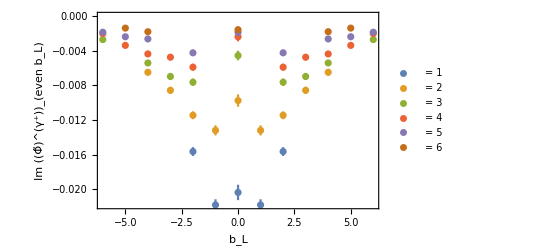

Fitting into   = -0.0175055 ⅇ^(-0.0336282 b_L^2-0.0633859 b_T^2)

Fit dependence in  space

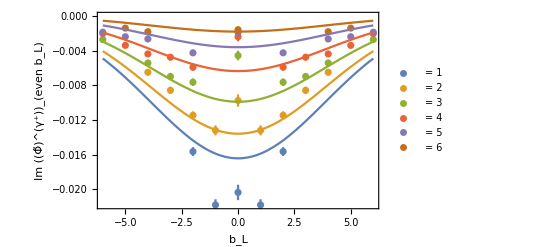

Cast in ,  space

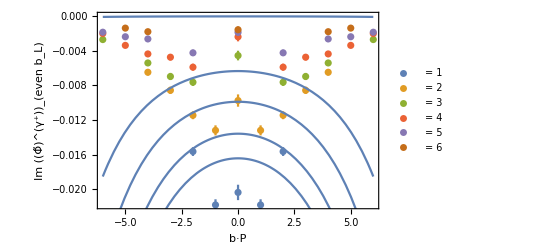

Fourier transform

-Graphics-

Normalize to -integrated Sivers shift, multiply by

-Graphics-

```mathematica
groupSameb=GroupBy[TablePlateauEvengPlusImForb,First->Last];
averagedTablePlateauEvengPlusImForb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
Print["✓ Same  with different linkPath are averaged\n"];
Print["     -even component of imaginary part of  correlator"];
bTlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,2]]];
bLlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,1]]];
PlotbLforDiffbTList={};
Do[
PlotbL2=Transpose[{Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTList,PlotbL2];
 ,{bT,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Print[PlotbL];
datafor2dGaussianFitbLbTerrors={};
Do[
dataPointErr=MakeErrBars[PlotbLforDiffbTList[[TagbT]]];
Do[
AppendTo[datafor2dGaussianFitbLbTerrors,{{dataPointErr[[All,1]][[TagbL]][[1]],bTlist[[TagbT]],dataPointErr[[All,1]][[TagbL]][[2]]},dataPointErr[[All,2,1]][[TagbL]]}];
,{TagbL,Length[dataPointErr]}];
,{TagbT,Length[bTlist]}];
points=datafor2dGaussianFitbLbTerrors[[All,1]];
errors=datafor2dGaussianFitbLbTerrors[[All,2]];
fitbLbLbT=NonlinearModelFit[points,A*Exp[-((alpha*()^2)+(beta*()^2))],{A,alpha, beta},{,},Weights->1/(errors[[All,2]]^2),Method->"LevenbergMarquardt",MaxIterations->10000];
Print["Fitting into   = ",Normal[fitbLbLbT]];
Print["\n             Fit dependence in  space"];
PlotfitbLbT=Show[PlotbL,Table[Plot[fitbLbLbT[x,bT],{x,Min[bLlist],Max[bLlist]},PlotStyle->ColorData[97,"ColorList"][[bT]]],{bT,1,Length[bTlist]}]];
Print[PlotfitbLbT];
Print["\n                 Cast in ,  space"];
FnbdotPbsqre[bp_,b2_]:=(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2^2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))];
bsquarelist={1,2,3,4, 10};
PlotbLdata= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Cast=Show[PlotbLdata,Table[Plot[FnbdotPbsqre[x,bsq],{x,Min[bLlist],Max[bLlist]}, Frame->True],{bsq,bsquarelist}]];
Print[Cast];
Print["\n                 Fourier transform "];
xFourierTransf[x_, b2_]:= FourierTransform[(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2^2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))],bp,x];
xFourier=Show[Table[Plot[xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
Print["\n    Normalize to -integrated Sivers shift, multiply by "];
xFourier=Show[Table[Plot[-x*xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
```

```mathematica
linkPathPbl = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->DistinctLinkPaths[[7]],numberFilter->Re}],sideNum];
Print["Total no. of sideNum = ",linkPathPbl//Length]
Print["Total no. of Distinct sideNum = ",linkPathPbl//CountDistinct]
DistinctSideNumPbl= DeleteDuplicates[linkPathPbl]
```

Total no. of sideNum = 50

Total no. of Distinct sideNum = 2

{0,1}

```mathematica
linkPathNbl = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->DistinctLinkPaths[[56]],numberFilter->Re}],sideNum];
Print["Total no. of sideNum = ",linkPathNbl//Length]
Print["Total no. of Distinct sideNum = ",linkPathNbl//CountDistinct]
DistinctSideNumNbl= DeleteDuplicates[linkPathNbl]
```

Total no. of sideNum = 637

Total no. of Distinct sideNum = 21

{0,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}

```mathematica
MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->DistinctLinkPaths[[7]],numberFilter->Re,sideNum-> 1}],sideNum]//Length
MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->DistinctLinkPaths[[7]],numberFilter->Re,sideNum-> 0}],sideNum]//Length
MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bveclinkPathsideNumLISTforbLpositive[[1,2]],sideNum-> bveclinkPathsideNumLISTforbLpositive[[1,3]][[1]]}],{sideExtent, sideLink, data}]
MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->DistinctLinkPaths[[7]],numberFilter->Re,sideNum-> 1}],{sideExtent, sideLink}]
```

25

25

{{0,{},⟨1.0971(13)⟩_(RowBox[{)},{0,{},⟨0.053(11)⟩_(RowBox[{)}}

{{0,{}},{1,{1}},{2,{1,3}},{3,{1,3,1}},{4,{1,3,1,3}},{5,{1,3,1,3,1}},{6,{1,3,1,3,1,3}},{7,{1,3,1,3,1,3,1}},{8,{1,3,1,3,1,3,1,3}},{9,{1,3,1,3,1,3,1,3,1}},{10,{1,3,1,3,1,3,1,3,1,3}},{11,{1,3,1,3,1,3,1,3,1,3,1}},{12,{1,3,1,3,1,3,1,3,1,3,1,3}},{-1,{-1}},{-2,{-1,-3}},{-3,{-1,-3,-1}},{-4,{-1,-3,-1,-3}},{-5,{-1,-3,-1,-3,-1}},{-6,{-1,-3,-1,-3,-1,-3}},{-7,{-1,-3,-1,-3,-1,-3,-1}},{-8,{-1,-3,-1,-3,-1,-3,-1,-3}},{-9,{-1,-3,-1,-3,-1,-3,-1,-3,-1}},{-10,{-1,-3,-1,-3,-1,-3,-1,-3,-1,-3}},{-11,{-1,-3,-1,-3,-1,-3,-1,-3,-1,-3,-1}},{-12,{-1,-3,-1,-3,-1,-3,-1,-3,-1,-3,-1,-3}}}

```mathematica
Do[Print[PathToShift[MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->DistinctLinkPaths[[7]],sideNum-> 0,numberFilter->Re}],sideLink][[i]],3]],{i,20, 25}]
Print[" "]
Do[Print[PathToShift[MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->DistinctLinkPaths[[7]],sideNum-> 1,numberFilter->Re}],sideLink][[i]],3]],{i,20, 25}]
```

{-3,0,-4}

{-4,0,-4}

{-4,0,-5}

{-5,0,-5}

{-5,0,-6}

{-6,0,-6}

{-4,0,-3}

{-4,0,-4}

{-5,0,-4}

{-5,0,-5}

{-6,0,-5}

{-6,0,-6}

```mathematica
linkPathforPbl = DistinctLinkPaths[[3]];
linkPathforNbl =DistinctLinkPaths[[3]];
sideNumforPbl = 45;
sideNumforNbl = 65;
blPg8Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->linkPathforPbl,sideNum-> sideNumforPbl,numberFilter->Re}],{sideExtent,data}];
blPg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->linkPathforPbl,sideNum-> sideNumforPbl,numberFilter->Im}],{sideExtent,data}];
blPg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->linkPathforPbl,sideNum-> sideNumforPbl,numberFilter->Re}],{sideExtent,data}];
blPg1Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->linkPathforPbl,sideNum-> sideNumforPbl,numberFilter->Im}],{sideExtent,data}];
blNg8Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->linkPathforNbl,sideNum-> sideNumforNbl,numberFilter->Re}],{sideExtent,data}];
blNg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->linkPathforNbl,sideNum-> sideNumforNbl,numberFilter->Im}],{sideExtent,data}];
blNg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->linkPathforNbl,sideNum-> sideNumforNbl,numberFilter->Re}],{sideExtent,data}];
blNg1Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->linkPathforNbl,sideNum-> sideNumforNbl,numberFilter->Im}],{sideExtent,data}];
etaList = blPg8Im[[All,1]];
blPgPlusRe = (-blPg1Im[[All, 2]]+blPg8Re[[All, 2]])/Sqrt[2];
blPgPlusIm = (blPg1Re[[All, 2]]+blPg8Im[[All, 2]])/Sqrt[2];
blNgPlusRe = (-blNg1Im[[All, 2]]+blNg8Re[[All, 2]])/Sqrt[2];
blNgPlusIm = (blNg1Re[[All, 2]]+blNg8Im[[All, 2]])/Sqrt[2];
blEvengPlusRe = (blPgPlusRe+blNgPlusRe)/2;
blEvengPlusIm = (blPgPlusIm+blNgPlusIm)/2;
blOddgPlusRe = (blPgPlusRe-blNgPlusRe)/2;
blOddgPlusIm = (blPgPlusIm-blNgPlusIm)/2;
PlotblEvengPlusRe=Transpose[{etaList,blEvengPlusRe}];
PlotblEvengPlusIm=Transpose[{etaList,blEvengPlusIm}];
PlotblOddgPlusRe=Transpose[{etaList,blOddgPlusRe}];
PlotblOddgPlusIm=Transpose[{etaList,blOddgPlusIm}];
plot1 = ErrorListPlot[MakeErrBars[PlotblEvengPlusRe],FrameLabel->{Style[η,Large],Style[,Large]}, Frame->True];
plot2 = ErrorListPlot[MakeErrBars[PlotblOddgPlusRe],FrameLabel->{Style[η,Large],Style[,Large]}, Frame->True];
plot3 = ErrorListPlot[MakeErrBars[PlotblEvengPlusIm],FrameLabel->{Style[η,Large],Style[,Large]}, Frame->True];
plot4 = ErrorListPlot[MakeErrBars[PlotblOddgPlusIm],FrameLabel->{Style[η,Large],Style[,Large]}, Frame->True];
GraphicsGrid[{{plot1,plot2},{plot3,plot4}}]
```

-Graphics-

Now, let’s reproduce preliminary plots from Dr. Engelhardt’s talk